# Monte-Carlo Simulation of Quantum wells

## Problem 1

```mathematica
ClearAll["Global`*"]
x0=-2;xf=2;dx=0.1;
x=Range[x0,xf,dx];lx=Length[x];
v=ConstantArray[1000000.,lx];
Do[If[-1<x⟦i⟧<1,v⟦i⟧=0.0],{i,0,lx}]
(*Construct an initial wavefunction*)
ψ=0*x;
Do[If[-1≤x⟦i⟧≤1,ψ⟦i⟧=1],{i,1,lx}]
(*Construct Hamiltonian*)
H=ConstantArray[0*x,lx];
H⟦1,{1,2}⟧={1/dx^2+v⟦1⟧,-1/(2 dx^2)};
H⟦lx,{lx-1,lx}⟧ = {-1/(2 dx^2),1/dx^2+v⟦lx⟧};
Do[H⟦i,{i-1,i,i+1}⟧=1/dx^2{-1/2,1+dx^2 v⟦i⟧,-1/2},{i,2,lx-1}]
ϵ=(ψ.H.ψ)/(ψ.ψ);|
(*Monte-Carlo Algorithm*)
Do[
ran=RandomInteger[{1,lx}];
ψtrial = ψ;
ψtrial⟦ran⟧+=RandomReal[{-0.2,0.2}];
ϵnew =(ψtrial.H.ψtrial)/(ψtrial.ψtrial);
If[ϵnew<ϵ,ψ=ψtrial/(√(dx ψtrial.ψtrial));ϵ=ϵnew],
{i,1,1000000}]
ϵ
```

Null|Null

1.23118

The same Eigenvalue is determined at in the third problem using the matrix method. Here this is in units of ((4 ℏ^2)/ma^2).

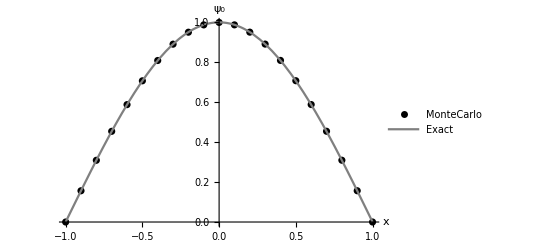

```mathematica
Show[
ListPlot[Table[{x⟦i⟧,ψ⟦i⟧},{i,1,lx}],PlotRange->{{-1,1},All},PlotStyle->Black,PlotLegends->{"MonteCarlo"}],
Plot[Cos[0.5π x],{x,-1,1},PlotStyle->Gray,PlotLegends->{"Exact"}]
,AxesLabel-> {"x","ψ_0"}
]
```

## Problem 2

Null|Null

0.667124

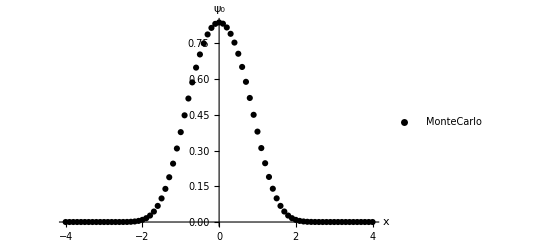

```mathematica
ClearAll["Global`*"]
x0=-4;xf=4;dx=0.1;
x=Range[x0,xf,dx];lx=Length[x];
v=x^4;
(*Construct an initial wavefunction*)
ψ=0*x;
Do[If[-1≤x⟦i⟧≤1,ψ⟦i⟧=1],{i,1,lx}]
(*Construct Hamiltonian*)
H=ConstantArray[0*x,lx];
H⟦1,{1,2}⟧={1/dx^2+v⟦1⟧,-1/(2 dx^2)};
H⟦lx,{lx-1,lx}⟧ = {-1/(2 dx^2),1/dx^2+v⟦lx⟧};
Do[H⟦i,{i-1,i,i+1}⟧=1/dx^2{-1/2,1+dx^2 v⟦i⟧,-1/2},{i,2,lx-1}]
ϵ=(ψ.H.ψ)/(ψ.ψ);|
(*Monte-Carlo Algorithm*)
Do[
ran=RandomInteger[{1,lx}];
ψtrial = ψ;
ψtrial⟦ran⟧+=RandomReal[{-0.2,0.2}];
ϵnew =(ψtrial.H.ψtrial)/(ψtrial.ψtrial);
If[ϵnew<ϵ,ψ=ψtrial/(√(dx ψtrial.ψtrial));ϵ=ϵnew],
{i,1,1000000}]

ϵ
ListPlot[Table[{x⟦i⟧,ψ⟦i⟧},{i,1,lx}],PlotStyle->Black,PlotLegends->{"MonteCarlo"},AxesLabel->{"x","ψ_0"}]
```

The ground state of the anharmonic potential is 0.667103 using MonteCarlo.

## Problem 3

Level | Matrix | Exact
1 | 1.23115 | 1.2337
2 | 4.8943 | 4.9348
3 | 10.8992 | 11.1033
4 | 19.0981 | 19.7392
5 | 29.2891 | 30.8425
6 | 41.2211 | 44.4132

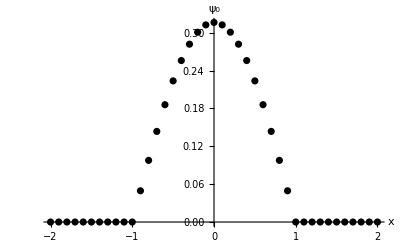

```mathematica
ClearAll["Global`*"]
x0=-2;xf=2;dx=0.1;
x=Range[x0,xf,dx];lx=Length[x];
v=ConstantArray[1000000.,lx];
Do[If[-1<x⟦i⟧<1,v⟦i⟧=0.0],{i,0,lx}]
(*Construct an initial wavefunction*)
ψ=0*x;
Do[If[-1≤x⟦i⟧≤1,ψ⟦i⟧=1],{i,1,lx}]
(*Construct Hamiltonian*)
H=ConstantArray[0*x,lx];
H⟦1,{1,2}⟧={1/dx^2+v⟦1⟧,-1/(2 dx^2)};
H⟦lx,{lx-1,lx}⟧ = {-1/(2 dx^2),1/dx^2+v⟦lx⟧};
Do[H⟦i,{i-1,i,i+1}⟧=1/dx^2{-1/2,1+dx^2 v⟦i⟧,-1/2},{i,2,lx-1}]

data = Prepend[Table[{n,Sort[Eigenvalues[H]]⟦n⟧,N[π^2/8(n)^2]},{n,1,6}],{"Level","Matrix", "Exact"}];
Grid[data,Frame->All]

ListPlot[Table[{x⟦i⟧,Eigenvectors[H]⟦-1,i⟧},{i,1,lx}],PlotStyle->Black,AxesLabel->{"x","ψ_0"}]
```

## Problem 4

```mathematica
ClearAll["Global`*"]
x0=-4;xf=4;dx=0.1;
x=Range[x0,xf,dx];lx=Length[x];
v=x^4;
(*Construct an initial wavefunction*)
ψ=0*x;
Do[If[-1≤x⟦i⟧≤1,ψ⟦i⟧=1],{i,1,lx}]
(*Construct Hamiltonian*)

H=ConstantArray[0*x,lx];
H⟦1,{1,2}⟧={1/dx^2+v⟦1⟧,-1/(2 dx^2)};
H⟦lx,{lx-1,lx}⟧ = {-1/(2 dx^2),1/dx^2+v⟦lx⟧};
Do[H⟦i,{i-1,i,i+1}⟧=1/dx^2{-1/2,1+dx^2 v⟦i⟧,-1/2},{i,2,lx-1}]
```

0.667048

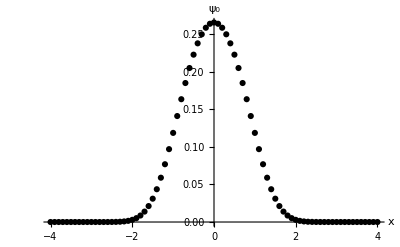

```mathematica
ψ=Eigenvalues[H]⟦-1⟧
ListPlot[Table[{x⟦i⟧,Eigenvectors[H]⟦-1,i⟧},{i,1,lx}],PlotStyle->Black,AxesLabel->{"x","ψ_0"}]
```

The ground state energy of the anharmonic potential is 0.667048 using the matrix method and 0.667103 using MonteCarlo.